```mathematica
(* this routine needs to run Vpots.nb *)
```

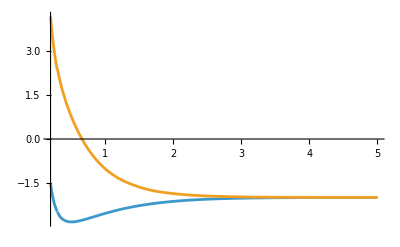

{0.35109,0.785517}

NDSolve::nlnum: The function value {0.999715,-9.28949-0.053124 e} is not a list of numbers with dimensions {2} at {r$13095,yg$13095[r$13095],yg$13095'[r$13095],NDSolve`s$13113[r$13095],NDSolve`s$13111[r$13095],NDSolve`s$13112[r$13095]} = {0.100028,0.0000284695,0.999715,1,-1,1}.

NDSolve::nlnum: The function value {0.999715,-8.96114-0.053124 e} is not a list of numbers with dimensions {2} at {r$13095,yu$13095[r$13095],yu$13095'[r$13095],NDSolve`s$13169[r$13095],NDSolve`s$13167[r$13095],NDSolve`s$13168[r$13095]} = {0.100028,0.0000284695,0.999715,1,-1,1}.

InterpolatingFunction::dmval: Input value {0.102041} lies outside the range of data in the interpolating function. Extrapolation will be used.

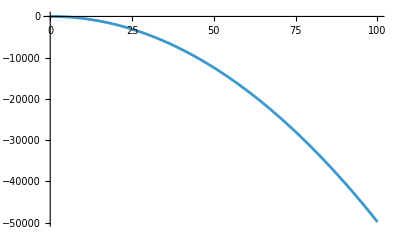

SetDelayed::write: Tag Times in Null ylogG$13095[r$_] is Protected.

InterpolatingFunction::dmval: Input value {100} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{Abs[(-0.122394+0.0150889 ylogG$13095[100.])/((-0.122394-0.0394256 ⅈ)+(0.0150889-0.0471537 ⅈ) ylogG$13095[100.])],0.949442}

```mathematica
geradeData=Import["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/gerade1sV3.mx"];
geradePotential=Table[{geradeData[[i,1]],geradeData[[i,3]]},{i,1,27}];
ungeradeData = Import["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/ungerade1sV3.mx"];
ungeradePotential=Table[{ungeradeData[[i,1]],ungeradeData[[i,3]]},{i,1,27}];
long[R_]:=-2.0-0.082/R^4;
geradefun=Interpolation[geradePotential];
ungeradefun=Interpolation[ungeradePotential];
(* Fit to a model *)
gdata=Drop[geradePotential,{5,27}];
udata=Drop[ungeradePotential,{5,27}];
model[R_,C1_,C2_,C3_]:=C1 Exp[-C2 R]/R+C3;
gnlm=NonlinearModelFit[gdata,model[R,C1,C2,C3],{C1,C2,C3},R];
unlm=NonlinearModelFit[udata,model[R,C1,C2,C3],{C1,C2,C3},R];
gshort[R_]:=model[R,C1,C2,C3] /. gnlm["BestFitParameters"];
ushort[R_]:=model[R,C1,C2,C3] /. unlm["BestFitParameters"];
gpot[R_]=Piecewise[{{gshort[R],R<=0.3},{geradefun[R],0.3<R<13.0},{long[R],R>=13.0}}];
upot[R_]=Piecewise[{{ushort[R],R<=0.3},{ungeradefun[R],0.3<R<13.0},{long[R],R>=13.0}}];
Plot[{gpot[R],upot[R]},{R,0.2,5},PlotRange->All]

(*e=0.1/27.21;*)
μ=1866.0/2.0;
(*k=√(2 μ e);*)
kB = 3.166^-6;  (* Boltzman, eV/K *)
(*λ=2π/k*)

r0=0.01;
rend=100;

computePhaseShifts[m_,e_,r0_,rend_]:=Module[{k,eqG,eqU,solsG,solsU,fg,fu},
k=√(2 μ e);
equG:=yg''[r]+yg'[r]/r-2 μ  (gpot[r]+2)yg[r]-m^2/r^2 yg[r]+2 μ e yg[r] ;
equU:=yu''[r]+yu'[r]/r-2 μ  (upot[r]+2)yu[r]-m^2/r^2 yu[r]+2 μ e yu[r]; 
solsG=Flatten[NDSolve[{equG==0,yg[r0]==0,yg'[r0]==1},yg,{r,r0,rend},MaxSteps->200000]];
solsU=Flatten[NDSolve[{equU==0,yu[r0]==0,yu'[r0]==1},yu,{r,r0,rend},MaxSteps->200000]];
fg[r_]=yg[r] /. solsG;
fu[r_]=yu[r] /. solsU;
(*Print[Plot[fg[r],{r,r0,rend}]];
Print[Plot[fu[r],{r,r0,rend}]];*)
(*Print[Plot[fg[r]-fu[r],{r,r0,rend}]]*)
ylogG[r_]:=fg'[r]/fg[r];
ylogU[r_]:=fu'[r]/fu[r];
(*Print[Plot[ylogG[r],{r,r0,rend}]];
Print[Plot[ylogU[r],{r,r0,rend}]];*)
sl[n_,r_]:=BesselJ[n,k r];
cl[n_,r_]:= HankelH1[n, k r];
slp[n_,r_]:=Derivative[0,1][sl][n,r];
clp[n_,r_]:=Derivative[0,1][cl][n,r];
bG[n_,r_]:=(-I)^(Abs[m])( slp[n,r]-ylogG[r] sl[n,r])/( clp[n,r]-ylogG[r]cl[n,r]);
bU[n_,r_]:=(-I)^(Abs[m])( slp[n,r]-ylogU[r] sl[n,r])/( clp[n,r]-ylogU[r]cl[n,r]);
(*N[Abs[bG[m,k,rend]-bU[m,k,rend]]]^2*)
{N[Abs[bG[m,rend]]],N[Abs[bU[m,rend]]]}
];
computePhaseShifts[10,0.003,0.1,100]
```

e=0.0992966, 0.00364927

NDSolve::nlnum: The function value {0.99971,-99.2012-0.00541654 e} is not a list of numbers with dimensions {2} at {r$64453,yg$64453[r$64453],yg$64453'[r$64453],NDSolve`s$64468[r$64453],NDSolve`s$64467[r$64453],NDSolve`s$64466[r$64453]} = {0.0100029,2.90276×10^-6,0.99971,1,1,-1}.

NDSolve::nlnum: The function value {0.99971,-99.3383-0.00541654 e} is not a list of numbers with dimensions {2} at {r$64453,yu$64453[r$64453],yu$64453'[r$64453],NDSolve`s$64509[r$64453],NDSolve`s$64508[r$64453],NDSolve`s$64507[r$64453]} = {0.0100029,2.90276×10^-6,0.99971,1,1,-1}.

InterpolatingFunction::dmval: Input value {100} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nlnum: The function value {0.99971,-99.1722-0.00541654 e} is not a list of numbers with dimensions {2} at {r$64545,yg$64545[r$64545],yg$64545'[r$64545],NDSolve`s$64558[r$64545],NDSolve`s$64559[r$64545],NDSolve`s$64560[r$64545]} = {0.0100029,2.90276×10^-6,0.99971,-1,1,1}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

e=0.109226, 0.0040142

e=0.119156, 0.00437912

e=0.129086, 0.00474405

e=0.139015, 0.00510898

e=0.148945, 0.0054739

e=0.158875, 0.00583883

e=0.168804, 0.00620376

e=0.178734, 0.00656869

e=0.188664, 0.00693361

e=0.198593, 0.00729854

100 | 0.
110 | 0.
120 | 0.
130 | 0.
140 | 0.
150 | 0.
160 | 0.
170 | 0.
180 | 0.
190 | 0.
200 | 0.

InterpolatingFunction::dmval: Input value {0.100018} lies outside the range of data in the interpolating function. Extrapolation will be used.

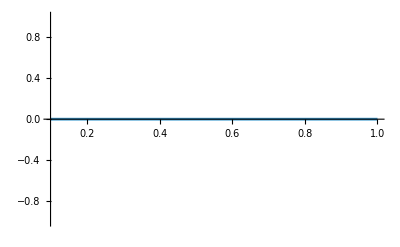

```mathematica
(* t = temperature, r0, rend - R range *)
computeCrossSect[t_,r0_,rend_]:= Module[{allBs,k,eV, eH},
eV= kB t;
eH = eV/27.21;
Print["e=",eV, ", ", eH];
k = √(2 μ eH);
allBs = Table[{m,computePhaseShifts[m,k,r0,rend]},{m,0,40}];
crossSection=1/k Total[allBs,{1}][[2]];
{t,crossSection}
];

crossSection = Table[computeCrossSect[t, r0, rend],{t, 100,130,10}];
crossSection // TableForm

crossSectionGraph = Interpolation[crossSection];

Plot[crossSectionGraph[t],{t, 0.1,1}]
```

Note the convergence of b_(m=40) as a function of R; b_(40) is already small, you need to calculate all b_{m} m<40, before total cross section sum over partial waves converges

The above code demonstrates the convergence of b_{m} (related to a phase shift) defined by Eq. (23) in my notes. This code is for the gerade potentials, do the same for the ungerade potentials, calculated in Vpots.nb. Use Eq. (38) in my notes to determine CRT cross sections.

You need to calculate b_{m} for many partial waves m, before σ  converges for large m (note above m=40, almost converged as |b_{40}|^2 <<1. You may want to re-write this code in python, to speed it up.

When complete, make a plot of the total cross sections, as a function of collision energy.
In order to educate the reader you may want to include additional figures, such as the dependence
of the partial wave cross sections, or plot of the wave function as shown above. Your thesis should be comprehensive and offer a narrative to help the, non-specialist reader, understand what and why you are doing.